-1+2/x^(1/3)

-2/(3 x^(4/3))

0<x<8

False

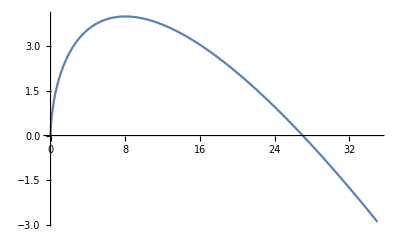

```mathematica
f[x_]:=3 x^(2/3)-x;
f'[x]//Simplify
f''[x]//Simplify
Reduce[f'[x]>0,x]
Reduce[f''[x]>0,x]
Plot[f[x],{x,0,35}]
```

```mathematica
f[8]
```

4